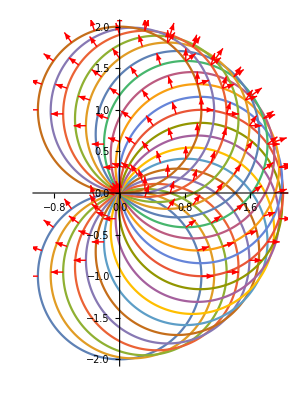

```mathematica
ParametricPlot[ 
Evaluate[
Table[
{ Cos[t] + Cos[s],  Sin[t] + Sin[s]}, {s, -Pi/2, Pi/2, Pi/20}
]
],
 {t, 0, 2Pi},
Epilog->{Red,Table[
Arrow[{
{ Cos[t] + Cos[s],  Sin[t] + Sin[s]},{ Cos[t] + Cos[s],  Sin[t] + Sin[s]}+.15{Cos[t],Sin[t]}
 }],
 {s, -Pi/2, Pi/2, Pi/10},
 {t, 0, Pi, Pi/10}
]}
]
```

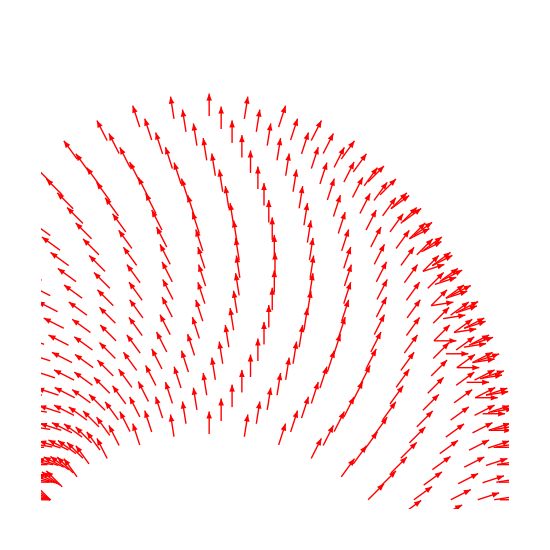

```mathematica
Show[Graphics[{Red,Table[
Arrow[{
{ Cos[t] + Cos[s],  Sin[t] + Sin[s]},{ Cos[t] + Cos[s],  Sin[t] + Sin[s]}+.1{Cos[t],Sin[t]}
 }],
 {s, -Pi/4,Pi/4, Pi/40},
 {t, 0, Pi, Pi/20}
]}], PlotRange->{{0,2},{0,2}}
]
```

```mathematica
StreamPlot[
n[x,y],
{x,y}∈ImplicitRegion[ x^2 + y^2 <= 4 && x >=0 && y>=0,{x,y}]
]
```

$Aborted

```mathematica
n[x_,y_] :={x,y} - First[{p,q}/.Assuming[{p>=0,q>0},
Solve[{(x-p)^2 + (y-q)^2 == 1, p^2 + q^2 ==1}, {p,q}]]];
```